### Lambda scan (c_hhh) & interpolation

```mathematica
Needs["ErrorBarPlots`"];

dataErr=Import["lambda-scan.csv","Data"];
data=Drop[dataErr,None,{3}];

dataErrEW=Import["lambda-scan_EWChL.csv","Data"];
dataEW=Drop[dataErrEW,None,{3}];
```

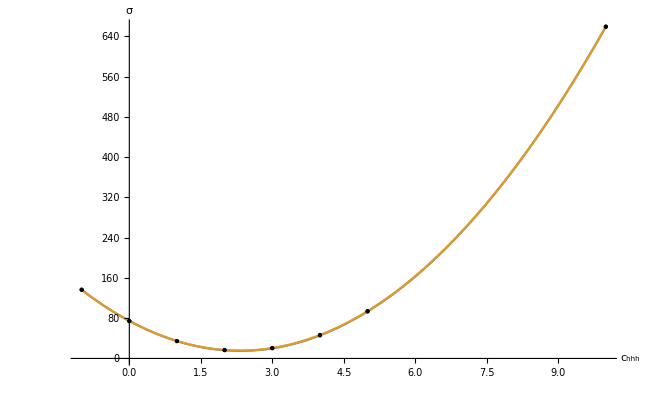

```mathematica
int=Fit[data,{1,x,x^2},x];
intEW=Fit[dataEW,{1,x,x^2},x];
Plot[{int,intEW},{x,-1,10},Epilog->{Point[data],Point[dataEW]},ImageSize->1000,AxesOrigin->{0,0},AxesLabel->{"c_hhh","σ"}]
```

```mathematica
Grid[dataErr, Alignment -> Left, Spacings -> {2, 1}, Frame -> All,ItemStyle->"Text"]
```

-1. | 136.67 | 0.753947
0. | 74.172 | 0.272243
1. | 34.4058 | 0.139012
2. | 16.3713 | 0.0682298
3. | 20.1128 | 0.102503
4. | 45.7604 | 0.26572
5. | 93.2583 | 0.556115
10. | 659.375 | 3.69115

```mathematica
Grid[dataErrEW, Alignment -> Left, Spacings -> {2, 1}, Frame -> All,ItemStyle->"Text"]
```

-1. | 136.449 | 0.694157
0. | 74.2049 | 0.204011
1. | 34.5665 | 0.0823395
2. | 16.8233 | 0.0771
3. | 20.724 | 0.10431
4. | 46.5625 | 0.23211
5. | 94.0164 | 0.332533
10. | 659.04 | 1.9091